# grid and integration

## 1. Global constants and basic functions

```mathematica
hbar=1.0545718176461565*10^-27;
e=4.803204712570263*10^(-10);
me=9.1093837015*10^(-28);
mp=1.67262192369*10^-24;
A=1;Z=1;Ye=1;
kb=1.380649*10^(-16);
kev2erg=1.6021766339999998*10^-9;
c=29979245800.0;
σT=8*π/3*e^4/(c^4 me^2);
κT=σT/mp;
G=6.674299999999999*10^-8;
Ms=1.988409870698051*10^33;
km=10^5;
αF=e^2/(hbar c);
BQ=me^2*c^3/e/hbar;
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
linearspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];
C0[a_]:=1/a-Exp[a]*ExpIntegralE[1,a];
C1[a_]:=(1+a)*Exp[a]*ExpIntegralE[1,a]-1;
radian[x_]:=x/180*π;
Planck[Es_,T_]:=2*hbar*2*π*(Es*kev2erg/hbar/2/π)^3/c^2*1/(Exp[(Es*kev2erg)/(kb*T)]-1);
```

## Temperature profile

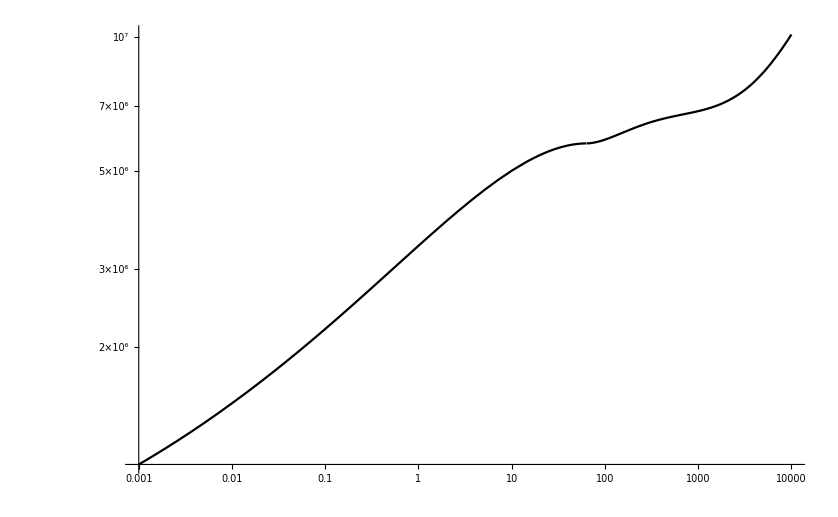

```mathematica
temperature[τ_]:=Module[{τmid,x},
τmid=63.2;
a1=0.761;
a2= 0.00198;
a3=0.267;
a4=−0.356;
a5= 0.179;
a6=−0.0282;
b3=−0.118;
b4=−0.0336;
b5=−0.00428;
b6=−0.00022;
x=Log[10,τ]-Log[10,τmid];
Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}]];
LogLogPlot[temperature[τ],{τ,0.001,10^4},Background->White,PlotTheme->"Monochrome"]
```

## Scatter opacity

```mathematica
Aint[Es_,B_,τ_]:=Module[{Ec,ω,ωc,Ece,Eci,Epe,Epi,ue,ui,ve,vi,b,a,q,m,ri,ϵp,ηp,g,ϵ,η,βi,K1i,K2i,Kz1i,Kz2i,ep1i,em1i,ep2i,em2i,e01i,e02i,Ap1,Am1,A01,Ap2,Am2,A02,Ap,Am,A0,ρ,x,T,Mns,Rns,gns,τmid},
τmid=63.2;
a1=0.761;
a2= 0.00198;
a3=0.267;
a4=−0.356;
a5= 0.179;
a6=−0.0282;
b3=−0.118;
b4=−0.0336;
b5=−0.00428;
b6=−0.00022;
x=Log[10,τ]-Log[10,τmid];
T=Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}];
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρ=mp*gns/(2*κT*kb*T)*τ;
Ec=Es*kev2erg;
ω=Ec/hbar;
ωc=(e B)/(me c);
Ece=hbar*ωc/kev2erg;
Eci=Ece*(Z me)/(A mp);
Epe=hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5/kev2erg;
Epi=((Z me)/(A mp))^0.5*Epe;
ue=(Ece/Es)^2;ui=(Eci/Es)^2;ve=(Epe/Es)^2;vi=(Epi/Es)^2;
b=B/BQ;
(*turn on the vacuum*)
a=1+αF/(2π)(1.195-2/3 Log[b]-1/b(0.8553+Log[b])-1/(2 b^2));
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
(*turn off the vacuum*)
(*a=1;
q=0;
m=0;*)
ϵp=1-(ve(1-(A mp)/(Z me) ui))/((1-ui)(1-ue));
ηp=1-ve;
g=(ve*ue^0.5)/((1-ui)(1-ue));
ϵ=ϵp+a-1;
η=ηp+a+q-1;
ri=1+m/a Sin[θi]^2;
βi=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θi]^2/Cos[θi];
K1i=βi(1-(1+ri/βi^2)^(1/2));
K2i=βi(1+(1+ri/βi^2)^(1/2));
Kz1i=(-((ϵp-ηp-q)*Sin[θi]Cos[θi]K1i + g * Sin[θi]))/(ϵp*Sin[θi]^2+(ηp+q)Cos[θi]^2+a-1);

Kz2i=(-((ϵp-ηp-q)*Sin[θi]Cos[θi]K2i + g * Sin[θi]))/(ϵp*Sin[θi]^2+(ηp+q)Cos[θi]^2+a-1);
ep1i=(1+K1i*Cos[θi]+Kz1i*Sin[θi])^2/(2(1+K1i^2+Kz1i^2));
ep2i=(1+K2i*Cos[θi]+Kz2i*Sin[θi])^2/(2(1+K2i^2+Kz2i^2));
em1i=(1-(K1i*Cos[θi]+Kz1i*Sin[θi]))^2/(2(1+K1i^2+Kz1i^2));
em2i=(1-(K2i*Cos[θi]+Kz2i*Sin[θi]))^2/(2(1+K2i^2+Kz2i^2));
e01i=(K1i * Sin[θi]-Kz1i*Cos[θi])^2/(1+K1i^2+Kz1i^2);
e02i=(K2i * Sin[θi]-Kz2i*Cos[θi])^2/(1+K2i^2+Kz2i^2);
Ap1=NIntegrate[3/4*Sin[θi]*ep1i,{θi,0,π}];
Am1=NIntegrate[3/4*Sin[θi]*em1i,{θi,0,π}];
A01=NIntegrate[3/4*Sin[θi]*e01i,{θi,0,π}];
Ap2=NIntegrate[3/4*Sin[θi]*ep2i,{θi,0,π}];
Am2=NIntegrate[3/4*Sin[θi]*em2i,{θi,0,π}];
A02=NIntegrate[3/4*Sin[θi]*e02i,{θi,0,π}];
{Ap1,Ap2,Am1,Am2,A01,A02}
]
```

```mathematica
Aint[1,5*10^14,1000]
```

{0.750076,0.146791,0.749924,0.14696,2.98298×10^-9,1.20625}

```mathematica
scatteropacity[Es_,B_,τ_,θb_]:=Module[{Ec,ω,ωc,Ece,Eci,Epe,Epi,ue,ui,ve,vi,b,a,q,m,r,ϵp,ηp,g,ϵ,η,β,K1,K2,Kz1,Kz2,ep1,em1,ep2,em2,e01,e02,ne,ni,gl,gp,y1,y2,ωci,α0,νre,νep,νem,νe0,νip,νim,νi0,sc11,sc12,sc21,sc22,τmid,x,T,ρ,Mns,Rns,gns},
τmid=63.2;
a1=0.761;
a2= 0.00198;
a3=0.267;
a4=−0.356;
a5= 0.179;
a6=−0.0282;
b3=−0.118;
b4=−0.0336;
b5=−0.00428;
b6=−0.00022;
x=Log[10,τ]-Log[10,τmid];
T=Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}];
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρ=mp*gns/(2*κT*kb*T)*τ;
Ec=Es*kev2erg;
ω=Ec/hbar;
ωc=(e B)/(me c);
ωci= (Z e B)/(A mp c);
Ece=hbar*ωc/kev2erg;Eci=Ece*(Z me)/(A mp);
Epe=hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5/kev2erg;
Epi=((Z me)/(A mp))^0.5*Epe;
ue=(Ece/Es)^2;ui=(Eci/Es)^2;ve=(Epe/Es)^2;vi=(Epi/Es)^2;
b=B/BQ;
(*turn on the vacuum*)
a=1+αF/(2π)(1.195-2/3 Log[b]-1/b(0.8553+Log[b])-1/(2 b^2));
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
(*turn off the vacuum*)
(*a=1;
q=0;
m=0;*)
r=1+m/a Sin[θb]^2;
ϵp=1-(ve(1-(A mp)/(Z me) ui))/((1-ui)(1-ue));
ηp=1-ve;
g=(ve*ue^0.5)/((1-ui)(1-ue));
ϵ=ϵp+a-1;
η=ηp+a+q-1;
β=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θb]^2/Cos[θb];
K1=β(1-(1+r/β^2)^(1/2));
K2=β(1+(1+r/β^2)^(1/2));
Kz1=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K1 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);

Kz2=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K2 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);
ep1=(1+K1*Cos[θb]+Kz1*Sin[θb])^2/(2(1+K1^2+Kz1^2));
ep2=(1+K2*Cos[θb]+Kz2*Sin[θb])^2/(2(1+K2^2+Kz2^2));
em1=(1-(K1*Cos[θb]+Kz1*Sin[θb]))^2/(2(1+K1^2+Kz1^2));
em2=(1-(K2*Cos[θb]+Kz2*Sin[θb]))^2/(2(1+K2^2+Kz2^2));
e01=(K1 * Sin[θb]-Kz1*Cos[θb])^2/(1+K1^2+Kz1^2);
e02=(K2 * Sin[θb]-Kz2*Cos[θb])^2/(1+K2^2+Kz2^2);
ne=ρ/mp;
ni=ne;
y1=hbar*ωc/(kb*T);
y2=ω/ωc;
gl=NIntegrate[Exp[-y1*y2*Sinh[x1]^2]*C1[y2*Exp[2 x1]],{x1,-Infinity,Infinity}];
gp=NIntegrate[Exp[-y1*y2*Sinh[x1]^2]*2*y2*Exp[2x1]C0[y2*Exp[2 x1]],{x1,-Infinity,Infinity}];
α0=4*π^2 Z^2 αF^3 (hbar^2 c^2)/me^2(2 me/(π kb T))^(1/2)(ne ni)/ω^3(1-Exp[(-hbar ω)/(kb *T)]);
νre=(2*e^2)/(3 me c^3)ω^2;
νep=νre+(α0*gl)/(ne σT)νre;
νem=νre+(α0*gl)/(ne σT)νre;
νe0=νre+(α0*gp)/(ne σT)νre;
νip=(νre+(α0*gl)/(ne σT)νre)me/mp;
νim=(νre+(α0*gl)/(ne σT)νre)me/mp;
νi0=(νre+(α0*gp)/(ne σT)νre)me/mp;

sc11=(ne σT)/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep1*Ap1+(ω^2/((ω-1*ωc)^2+νem^2))em1*Am1+(ω^2/((ω+0*ωc)^2+νe0^2))e01*A01)+(me/mp)^2(ne σT)/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep1*Ap1+(ω^2/((ω+1*ωci)^2+νim^2))em1*Am1+(ω^2/((ω+0*ωci)^2+νi0^2))e01*A01);

sc12=(ne σT)/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep1*Ap2+(ω^2/((ω-1*ωc)^2+νem^2))em1*Am2+(ω^2/((ω+0*ωc)^2+νe0^2))e01*A02)+(me/mp)^2(ne σT)/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep1*Ap2+(ω^2/((ω+1*ωci)^2+νim^2))em1*Am2+(ω^2/((ω+0*ωci)^2+νi0^2))e01*A02);
sc21=(ne σT)/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep2*Ap1+(ω^2/((ω-1*ωc)^2+νem^2))em2*Am1+(ω^2/((ω+0*ωc)^2+νe0^2))e02*A01)+(me/mp)^2(ne σT)/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep2*Ap1+(ω^2/((ω+1*ωci)^2+νim^2))em2*Am1+(ω^2/((ω+0*ωci)^2+νi0^2))e02*A01);

sc22=(ne σT)/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep2*Ap2+(ω^2/((ω-1*ωc)^2+νem^2))em2*Am2+(ω^2/((ω+0*ωc)^2+νe0^2))e02*A02)+(me/mp)^2(ne σT)/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep2*Ap2+(ω^2/((ω+1*ωci)^2+νim^2))em2*Am2+(ω^2/((ω+0*ωci)^2+νi0^2))e02*A02);
{sc11,sc12,sc21,sc22}

]
```

```mathematica
{Ap1,Ap2,Am1,Am2,A01,A02}=Aint[1,5*10^14,100]
scatteropacity[1,5*10^14,100,π/100]
```

{0.750161,0.240846,0.749839,0.24117,3.62212×10^-9,1.01798}

{2.13207×10^-8,2.11965×10^-7,2.0695×10^-8,0.000437065}

## free free opacity

```mathematica
freeopacity[Es_,B_,τ_,θb_]:=Module[{Ec,ω,ωc,Ece,Eci,Epe,Epi,ue,ui,ve,vi,b,a,q,m,r,ϵp,ηp,g,ϵ,η,β,K1,K2,Kz1,Kz2,ep1,em1,ep2,em2,e01,e02,ne,ni,α0,gl,gp,y1,y2,ωci,νre,νep,νem,νe0,νip,νim,νi0,ffe1,ffi1,ffe2,ffi2,ff1,ff2,T,ρ,Mns,Rns,gns,τmid,x},
τmid=63.2;
a1=0.761;
a2= 0.00198;
a3=0.267;
a4=−0.356;
a5= 0.179;
a6=−0.0282;
b3=−0.118;
b4=−0.0336;
b5=−0.00428;
b6=−0.00022;
x=Log[10,τ]-Log[10,τmid];
T=Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}];
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρ=mp*gns/(2*κT*kb*T)*τ;
Ec=Es*kev2erg;
ω=Ec/hbar;
ωc=(e B)/(me c);
ωci= (Z e B)/(A mp c);
Ece=hbar*ωc/kev2erg;Eci=Ece*(Z me)/(A mp);
Epe=hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5/kev2erg;
Epi=((Z me)/(A mp))^0.5*Epe;
ue=(Ece/Es)^2;ui=(Eci/Es)^2;ve=(Epe/Es)^2;vi=(Epi/Es)^2;
b=B/BQ;
(*turn on the vacuum*)
a=1+αF/(2π)(1.195-2/3 Log[b]-1/b(0.8553+Log[b])-1/(2 b^2));
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
(*turn off the vacuum*)
(*a=1;
q=0;
m=0;*)
r=1+m/a Sin[θb]^2;
ϵp=1-(ve(1-(A mp)/(Z me) ui))/((1-ui)(1-ue));
ηp=1-ve;
g=(ve*ue^0.5)/((1-ui)(1-ue));
ϵ=ϵp+a-1;
η=ηp+a+q-1;
β=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θb]^2/Cos[θb];
K1=β(1-(1+r/β^2)^(1/2));
K2=β(1+(1+r/β^2)^(1/2));
Kz1=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K1 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);

Kz2=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K2 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);
ep1=(1+K1*Cos[θb]+Kz1*Sin[θb])^2/(2(1+K1^2+Kz1^2));
ep2=(1+K2*Cos[θb]+Kz2*Sin[θb])^2/(2(1+K2^2+Kz2^2));
em1=(1-(K1*Cos[θb]+Kz1*Sin[θb]))^2/(2(1+K1^2+Kz1^2));
em2=(1-(K2*Cos[θb]+Kz2*Sin[θb]))^2/(2(1+K2^2+Kz2^2));
e01=(K1 * Sin[θb]-Kz1*Cos[θb])^2/(1+K1^2+Kz1^2);
e02=(K2 * Sin[θb]-Kz2*Cos[θb])^2/(1+K2^2+Kz2^2);
ne=ρ/mp;
ni=ne;
α0=4*π^2 Z^2 αF^3 (hbar^2 c^2)/me^2(2 me/(π kb T))^(1/2)(ne ni)/ω^3(1-Exp[(-hbar ω)/(kb *T)]);
y1=hbar*ωc/(kb*T);
y2=ω/ωc;
gl=NIntegrate[Exp[-y1*y2*Sinh[x1]^2]*C1[y2*Exp[2 x1]],{x1,-Infinity,Infinity}];
gp=NIntegrate[Exp[-y1*y2*Sinh[x1]^2]*2*y2*Exp[2x1]C0[y2*Exp[2 x1]],{x1,-Infinity,Infinity}];
νre=(2*e^2)/(3 me c^3)ω^2;
νep=νre+(α0*gl)/(ne σT)νre;
νem=νre+(α0*gl)/(ne σT)νre;
νe0=νre+(α0*gp)/(ne σT)νre;
νip=(νre+(α0*gl)/(ne σT)νre)me/mp;
νim=(νre+(α0*gl)/(ne σT)νre)me/mp;
νi0=(νre+(α0*gp)/(ne σT)νre)me/mp;
ffe1=α0/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep1*gl+(ω^2/((ω-1*ωc)^2+νem^2))em1*gl+(ω^2/((ω+0*ωc)^2+νe0^2))e01*gp);
ffi1=1/Z^3((Z^2 me)/(A mp))^2 α0/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep1*gl+(ω^2/((ω+1*ωci)^2+νim^2))em1*gl+(ω^2/((ω+0*ωci)^2+νi0^2))e01*gp);
ffe2=α0/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep2*gl+(ω^2/((ω-1*ωc)^2+νem^2))em2*gl+(ω^2/((ω+0*ωc)^2+νe0^2))e02*gp);
ffi2=1/Z^3((Z^2 me)/(A mp))^2 α0/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep2*gl+(ω^2/((ω+1*ωci)^2+νim^2))em2*gl+(ω^2/((ω+0*ωci)^2+νi0^2))e02*gp);


ff1=ffe1+ffi1;
ff2=ffe2+ffi2;
{ff1,ff2}

]
```

## jump condition

```mathematica
τreson[Es_,B_]:=Module[{q,m,ωc,Ebi,Mns,Rns,Ead,b,δv,fB,gns,ρv,τv},
b=B/BQ;
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
δv=αF/(45*π)b^2;
fB=((3*δv)/(q+m))^0.5;
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρv=0.96* Ye^-1(Es/1)^2(B/10^14)^2 fB^-2;
τv=τx/.FindRoot[temperature[τx]-τx*(mp gns)/(κT 2 ρv kb)==0 ,{τx,((mp gns)/(κT 2 ρv kb*5*10^6))^-1}];
τv]

Pjump[Es_,B_,θb_]:=Module[{τv,Tv,Hρ,jump,b,q,m,δv,fB,Mns,Rns,gns,ωc,Ebi,ρv,Ead},

b=B/BQ;
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
δv=αF/(45*π)b^2;
fB=((3*δv)/(q+m))^0.5;
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ωc=(e B)/(me c);
Ebi=hbar*ωc*me/mp/kev2erg;
ρv=0.96* Ye^-1(Es/1)^2(B/10^14)^2 fB^-2;
τv=τx/.FindRoot[temperature[τx]-τx*(mp gns)/(κT 2 ρv kb)==0 ,{τx,((mp gns)/(κT 2 ρv kb*5*10^6))^-1}];
Tv=temperature[τv];

Hρ=Abs[2*kb*Tv/(mp * gns *Cos[θb])];
Ead=2.52*((fB*Tan[θb])^2)^(1/3)*(Abs[1-(Ebi/Es)^2])^(2/3)(1/Hρ)^(1/3);
jump=Exp[-π/2(Es/Ead)^3];
N[jump]
]
```

## Generating the grid

```mathematica
Es=3;
B=5*10^14;
τv=τreson[Es,B];
τx1=logspace[-3,Log[10,τv],(IntegerPart[Log[10,τv]]+3)*20];
τx2=logspace[Log[10,τv],Log[10,2]+4,IntegerPart[(Log[10,2]+4-Log[10,τv])]*20];
τ=Reverse[DeleteDuplicates[Flatten[{τx1,τx2}]]];
position=IntegerPart[(Log[10,2]+4-Log[10,τv])]*20;
θx=N[Range[0.001,89.9,(89.9-0.001)/30]]/180*π;
I1u=Table[0,Length[τ],Length[θx]];
I2u=Table[0,Length[τ],Length[θx]];
I1d=Table[0,Length[τ],Length[θx]];
I2d=Table[0,Length[τ],Length[θx]];
I1u[[1]]=Flatten[Table[1/2,1,Length[θx]]*Planck[Es,temperature[First[τ]]]];
I2u[[1]]=Flatten[Table[1/2,1,Length[θx]]*Planck[Es,temperature[First[τ]]]];
I1d[[Length[τ]]]=Flatten[Table[0,1,Length[θx]]];
I2d[[Length[τ]]]=Flatten[Table[0,1,Length[θx]]];
(*give the initial data for source function*)
S1=Table[0,Length[τ],Length[θx]];
S2=Table[0,Length[τ],Length[θx]];

u1=Table[0,Length[τ]];
u2=Table[0,Length[τ]];
δτ=Table[0,Length[τ]];
δτ1=Table[0,Length[τ]];
For[j=1,j≤Length[θx],j++,
For[
i=1,i≤Length[τ],i++,S1[[i,j]]=1/2*Planck[Es,temperature[τ[[i]]]];S2[[i,j]]=1/2*Planck[Es,temperature[τ[[i]]]]];
]
```

```mathematica
ff1=Table[0,{Length[τ]},{Length[θx]}];
ff2=Table[0,{Length[τ]},{Length[θx]}];
sc11=Table[0,{Length[τ]},{Length[θx]}];
sc12=Table[0,{Length[τ]},{Length[θx]}];
sc21=Table[0,{Length[τ]},{Length[θx]}];
sc22=Table[0,{Length[τ]},{Length[θx]}];
κt1=Table[0,Length[τ],Length[θx]];
κt2=Table[0,Length[τ],Length[θx]];
For[i=1,i≤Length[τ],i++,
{Ap1,Ap2,Am1,Am2,A01,A02}=Aint[Es,B,τ[[i]]];
For[j=1,j≤Length[θx],j++,
free=freeopacity[Es,B,τ[[i]],θx[[j]]];
ff1[[i,j]]=free[[1]];ff2[[i,j]]=free[[2]];
scatter=scatteropacity[Es,B,τ[[i]],θx[[j]]];
sc11[[i,j]]=scatter[[1]];
sc12[[i,j]]=scatter[[2]];
sc21[[i,j]]=scatter[[3]];
sc22[[i,j]]=scatter[[4]];
κt1[[i,j]]=ff1[[i,j]]+sc11[[i,j]]+sc12[[i,j]];
κt2[[i,j]]=ff2[[i,j]]+sc21[[i,j]]+sc22[[i,j]];
]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θi near {θi} = {2.0064}. NIntegrate obtained 6.71855×10^-12 and 7.04698×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θi near {θi} = {1.87141}. NIntegrate obtained 5.5263×10^-12 and 9.12812×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θi near {θi} = {1.66279}. NIntegrate obtained 3.73426×10^-12 and 7.65946×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
For[k=1,k≤15,k++,
For[j=1,j≤Length[θx],j++,
θ=θx[[j]];μ=Cos[θ];
(*upward integration and downward integration*)
For[i=2,i≤Length[τ],i++,
δτ[[i]]=τ[[i]]-τ[[i-1]];
I1u[[i,j]]=1/(1-(δτ[[i]]* κt1[[i,j]])/(2*μ*κT))((1+(δτ[[i]]* κt1[[i-1,j]])/(2*μ*κT))I1u[[i-1,j]]-δτ[[i]]/(2*μ*κT)*(κt1[[i-1,j]]*S1[[i-1,j]]+κt1[[i,j]]*S1[[i,j]]));
I2u[[i,j]]=1/(1-(δτ[[i]]* κt2[[i,j]])/(2*μ*κT))((1+(δτ[[i]]* κt2[[i-1,j]])/(2*μ*κT))I2u[[i-1,j]]-δτ[[i]]/(2*μ*κT)*(κt2[[i-1,j]]*S2[[i-1,j]]+κt2[[i,j]]*S2[[i,j]]));
ax=I1u[[i,j]];
bx=I2u[[i,j]];
If[i==position,
I1u[[i,j]]=Pjump[Es,B,θ]*ax+(1-Pjump[Es,B,θ])*bx;
I2u[[i,j]]=Pjump[Es,B,θ]*bx+(1-Pjump[Es,B,θ])*ax,
I1u[[i,j]]=ax;I2u[[i,j]]=bx
];

i1=Length[τ]+1-i;
δτ1[[i1]]=τ[[i1]]-τ[[i1+1]];
I1d[[i1,j]]=1/(1+(δτ1[[i1]]* κt1[[i1,j]])/(2*μ*κT))((1-(δτ1[[i1]]* κt1[[i1+1,j]])/(2*μ*κT))I1d[[i1+1,j]]+δτ1[[i1]]/(2*μ*κT)*(κt1[[i1+1,j]]*S1[[i1+1,j]]+κt1[[i1,j]]*S1[[i1,j]]));
I2d[[i1,j]]=1/(1+(δτ1[[i1]]* κt2[[i1,j]])/(2*μ*κT))((1-(δτ1[[i1]]* κt2[[i1+1,j]])/(2*μ*κT))I2d[[i1+1,j]]+δτ1[[i1]]/(2*μ*κT)*(κt2[[i1+1,j]]*S2[[i1+1,j]]+κt2[[i1,j]]*S2[[i1,j]]));
ay=I1d[[i1,j]];
by=I2d[[i1,j]];
If[i1==Length[τ]+1-position,
I1d[[i1,j]]=Pjump[Es,B,θ]*ay+(1-Pjump[Es,B,θ])*by;
I2d[[i1,j]]=Pjump[Es,B,θ]*by+(1-Pjump[Es,B,θ])*ay,
I1d[[i1,j]]=ay;I2d[[i1,j]]=by
];
];

];
For[m=1,m≤Length[τ],m++,
u1[[m]]=2*π/c*(Integrate[Interpolation[Transpose@{θx,Sin[θx]*(I1u[[m]]+I1d[[m]])},InterpolationOrder->1][t],{t,Min[θx],Max[θx]}]);
u2[[m]]=2*π/c*Integrate[Interpolation[Transpose@{θx,Sin[θx]*(I2u[[m]]+I2d[[m]])},InterpolationOrder->1][t],{t,Min[θx],Max[θx]}];
S1[[m]]=ff1[[m]]/κt1[[m]]*Planck[Es,temperature[τ[[m]]]]/2+sc11[[m]]/κt1[[m]]*(c u1[[m]])/(4 π)+sc12[[m]]/κt1[[m]]*(c u2[[m]])/(4 π);
S2[[m]]=ff2[[m]]/κt2[[m]]*Planck[Es,temperature[τ[[m]]]]/2+sc21[[m]]/κt2[[m]]*(c u1[[m]])/(4 π)+sc22[[m]]/κt2[[m]]*(c u2[[m]])/(4 π);

]
]
```

General::munfl: Exp[-1.15662×10^12] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
I1u[[-1]]
```

{36309.5,7729.,7119.51,7137.76,7225.63,7312.46,7388.76,7468.31,7569.,7700.95,7865.17,8056.92,8269.28,8495.4,8729.51,8967.19,9205.16,9440.95,9672.35,9896.84,10110.7,10308.,10478.1,10602.9,10650.2,10563.,10242.2,9525.82,8224.65,6478.65,2644.88}

```mathematica
I2u[[-1]]
```

{9883.03,6473.42,4570.46,3375.31,2527.22,1933.49,1514.15,1213.9,995.944,835.661,716.375,626.604,558.32,505.834,465.069,433.065,407.654,387.232,370.601,356.857,345.312,335.433,326.805,319.093,312.027,305.382,298.982,292.734,286.771,281.76,271.062}

```mathematica
(I1u[[-1]]+I2u[[-1]])Cos[θx]
```

{46192.5,14183.,11626.1,10383.9,9540.17,8931.56,8468.09,8106.77,7826.04,7608.15,7434.28,7285.59,7145.25,6999.5,6837.85,6652.72,6438.82,6192.57,5911.55,5594.01,5238.5,4843.54,4407.34,3927.69,3402.02,2828.19,2207.21,1551.17,903.463,365.198,5.08928}

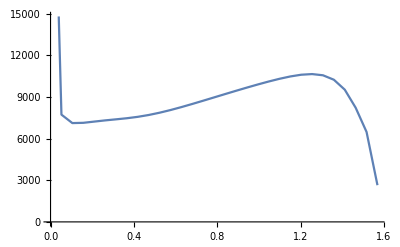

```mathematica
data=Transpose@{θx,I1u[[-1]]};
ListPlot[data,Joined->True]
```

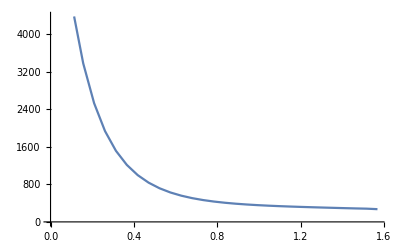

```mathematica
data=Transpose@{θx,I2u[[-1]]};
ListPlot[data,Joined->True]
```

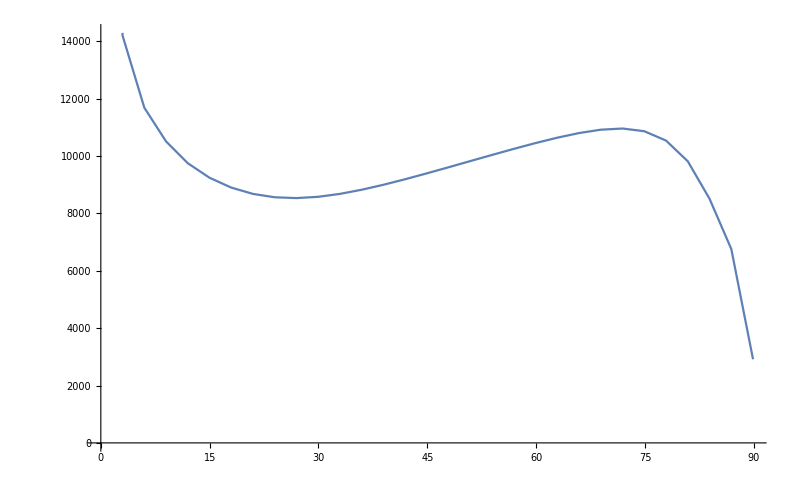

```mathematica
data=Transpose@{θx/π*180,I1u[[-1]]+I2u[[-1]]};
ListPlot[data,Joined->True]
```

```mathematica
data=Transpose@{θx,I1u[[-1]],I2u[[-1]]};
SetDirectory[NotebookDirectory[]]
Export["second.dat",data];
```

/Users/yonggao/Desktop/paper_calc/X-ray

```mathematica
I1u[[1]]
```

{203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.,203025.}

```mathematica
I1d[[1]]
```

{202998.,203022.,203020.,203017.,203012.,203008.,203003.,203000.,202997.,202994.,202992.,202991.,202991.,202990.,202991.,202991.,202992.,202994.,202995.,202997.,202999.,203001.,203003.,203006.,203008.,203011.,203014.,203016.,203019.,203022.,203025.}